## Chapter 0: Functions and exports

```mathematica
Needs["CoolTools`"]
Needs["Carlos`"]
Needs["Quantum`"]
Needs["ThesisTools`"]
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
PNGSetToGif[set_,name_]:=Export["../figures/"<>name<>".gif",
Flatten[{set, Table[set[[i]], {i, Length[set]}]}]];
FunctionSphereMesh2[r_,function_,opa_:1.]:=Show[
ParametricPlot3D[function[{r*Sin[t] Cos[p], r*Sin[t] Sin[p], r*Cos[t]}], {t, 0, π}, {p, 0, 2 π}, 
Lighting -> {"Neutral", White},
PlotStyle -> {GrayLevel[.3],Opacity[opa]}, 
PlotTheme -> None,
BoxRatios->{1, 1, 1},
PlotRange->{{-1.,1.},{-1.,1.},{-1.,1.}},
AxesLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{x}","r_{y}","r_{z}"},
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize}],
ParametricPlot3D[function[{r*Cos[t],r*Sin[t],0}],{t,0,2*Pi},PlotStyle->Red],
ListPointPlot3D[(Map[function[#]&,{{0,0,r},{0,0,-r}}]),PlotStyle->{Red,PointSize[0.03]}]]
Fontsize=18;
CircleTimes=KroneckerProduct;
```

## Chapter 3: MaxEntAss and its evolution

```mathematica
(*This graphs the radius of the effective state as a function of the Lagrange multiplier*)
RLambda=Plot[
	Evaluate[
		Map[(RadiusAsFunctionOfLagrange[λ,{p,1-p}]/.{p->#})&,{0.1,0.2,0.3,0.5}]],
	{λ,0,8},
	PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Darker[Green]}},
	PlotTheme->"FrameGrid",
PlotRange->All,
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"\\lambda","r_{\\text{ef}}"},
FrameStyle->Black,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize},
	PlotLegends->Placed[(MaTeX[#,FontSize->Fontsize]&)/@Map["p="<>ToString[#]&,{0.1,0.2,0.3,0.5}],{0.8,0.45}]]
```

```mathematica
label="r(lambda)";
Export["../notes/thesis/chapter2/figures/"<>label<>".pdf",RLambda]
```

## Chapter 4: Effective Dynamics

## 4.1 Local evolutions

```mathematica
(*Parameters: number of particles, probability vector, frecuencies*)
NumberOfParticles =10;
p1 = 0.95;
pk = (1-p1)/(NumberOfParticles-1);
pBoltz=Table[1/NumberOfParticles,NumberOfParticles];
pPref= Join[{p1}, Table[pk,NumberOfParticles-1]];
ωallnorm = RandomVariate[NormalDistribution[μ=2*Pi, σ=0.5], NumberOfParticles];ωallnorm[[1]]=2*Pi;
ωallunif= RandomVariate[UniformDistribution[{a=1,b=3}],NumberOfParticles];ωallunif[[1]]=1.5;
ωprefinveq=Table[2*Pi,NumberOfParticles];ωprefinveq[[1]]=0;
ωprefinran=RandomVariate[UniformDistribution[{a=-3,b=3}],NumberOfParticles];ωprefinran[[1]]=0;
ωnpinv=0;
```

```mathematica
(*Initial effective state*)
ω=ωallunif;
ρef = (IdentityMatrix[2] + (rp=0.9)* ({x,y,z}=Normalize[{1., 1., 0.1}]).Rest[NQubitBasis[1]])/2;
ref = densityMatrixToPoint[{ρef}, NQubitBasis[1]];
```

```mathematica
(*Dynamics functions*)
u[k_, t_, om_]:= MatrixExp[-I t om[[k]] *PauliMatrix[3]];
Γ[rho_, omegas_, p_, t_]:=  
With[{n = Length[omegas], σ = PauliMatrix[3], ρjs = MaxEntSubStates[rho, p]}, 
	 Sum[p[[j]] (u[j,t,omegas].ρjs[[j]].Dagger[u[j,t,omegas]]), {j,n}] ];
BVEvolution[init_, ω_, p_, t_]:= densityMatrixToPoint[{Γ[init, ω, p, t]}, NQubitBasis[1]][[1]];
(*Bloch vector function*)
BVt[t_] = BVEvolution[ρef,ω,pPref,t];
```

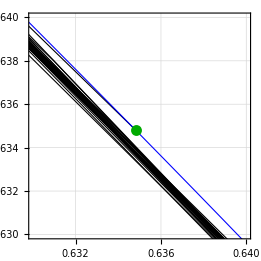

```mathematica
(*Plot of the trajectory of the effective Bloch Vector*)
BVTraj=Show[ParametricPlot[BVt[t][[1;;2]],
{t,tini=0,tend=50},
PlotTheme->"FrameGrid",
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{x}","r_{y}"},
PlotStyle->{Thickness[0.003],Black},
FrameStyle->Black,
PlotRange->{{0.63,0.64},{0.63,0.64}}(*Full/All*),
AspectRatio->Automatic,
	LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize},
PlotLabel->(MaTeX[#,FontSize->Fontsize+5]&["p_{1}="<>ToString[p1]<>", n="<>ToString[NumberOfParticles]]),
Epilog->{Darker[Green],PointSize[0.03],Point[BVt[tini][[1;;2]]]}],
ParametricPlot[RotationTransform[4*Pi*t,{0,0,1}][BVt[tini]][[1;;2]],{t,tini=0,tend=0.5},
PlotStyle->{Thickness[0.003],Blue}]]
```

```mathematica
(*Exporting*)
label1="local_all_ran"<>"_p="<>ToString[p1]<>"_r="<>ToString[rp]<>"_n="<>ToString[NumberOfParticles]<>"_a="<>ToString[a]<>"_b="<>ToString[b];
Export["../thesis/chapter3/figures_separable/"<>label1<>".pdf",BVTraj,ImageSize->{480,480}]
```

../thesis/chapter3/figures_separable/local_all_ran_p=0.95_r=0.9_n=10_a=-3_b=3.pdf

```mathematica
Refine[SU2ToSO3[MatrixExp[-I*t*PauliMatrix[3]]],Element[t,Reals]]//FullSimplify
```

```mathematica
(*Graphs for the evolution of sigma3 x Id*)
DephasingTransform[r_,p_,ω_,t_]:=p.{r,RotationTransform[ω*t,{0,0,1}]@r}
PrefPauli3AndInvariantNPTransform[r_,p_,ω_,t_]:=With[{rhat=Normalize[r],λ=LagrangeMulFromRadius[Norm[r],p]},p.{RotationTransform[ω*t,{0,0,1}]@(Tanh[λ*p[[1]]]*rhat),Tanh[λ*p[[2]]]*rhat}]
time=0.0;
rad=0.9;
pvec={0.6,0.4};
plot=FunctionSphereMesh2[rad,PrefPauli3AndInvariantNPTransform[#,pvec,2*Pi,time]&,1.]
Export["../thesis/chapter3/figures_separable/szxId_t="<>ToString[time]<>"_p="<>ToString[pvec[[1]]]<>"_r="<>ToString[rad]<>".png",plot];
```

## 4.2 Quantum gates

### SWAP gate

```mathematica
Fontsize=18;
KLambdaPlot=Plot[
	Evaluate[
		Map[(SWAPContractionFactor[1,p,λ]/.{p->#})&,{0.1,0.2,0.3,0.5}]],
	{λ,0,20},
	PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Darker[Green]}},
	PlotTheme->"FrameGrid",
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"\\lambda","\\kappa_{1}^{\\rho_{\\text{ef}}}"},
FrameStyle->Black,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
	PlotLegends->Placed[(MaTeX[#,FontSize->Fontsize]&)/@Map["p="<>ToString[#]&,{0.1,0.2,0.3,0.5}],{0.8,0.45}]];
label="K(lambda)";
Export["../thesis/chapter3/figures_toy/"<>label<>".pdf",KLambdaPlot]
```

../thesis/chapter3/figures_toy/K(lambda).pdf

```mathematica
KRPlot=Plot[
	Evaluate[
		Map[(SWAPContractionFactor[1,p,LagrangeMulFromRadius[r,{p,1-p}]]/.{p->#})&,{0.1,0.2,0.3,0.5}]],
	{r,0,0.99},
	PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Darker[Green]}},
	PlotTheme->"FrameGrid",
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{\\text{ef}}","\\kappa_{1}^{\\rho_{\\text{ef}}}"},
FrameStyle->Black,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5}];
label="K(r)";
Export["../thesis/chapter3/figures_toy/"<>label<>".pdf",KRPlot]
```

FindRoot::nlnum: The function value {0.-1. r} is not a list of numbers with dimensions {1} at {CoolTools`Private`l} = {0.}.

ReplaceAll::reps: {FindRoot[RadiusAsFunctionOfLagrange[CoolTools`Private`l,{p,1-p}]==r,{CoolTools`Private`l,0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. r} is not a list of numbers with dimensions {1} at {CoolTools`Private`l} = {0.}.

ReplaceAll::reps: {FindRoot[RadiusAsFunctionOfLagrange[CoolTools`Private`l,{p,1-p}]==r,{CoolTools`Private`l,0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. r} is not a list of numbers with dimensions {1} at {CoolTools`Private`l} = {0.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[RadiusAsFunctionOfLagrange[CoolTools`Private`l,{p,1-p}]==r,{CoolTools`Private`l,0}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

../thesis/chapter3/figures_toy/K(r).pdf

```mathematica
KtPlot=Plot[
	Evaluate[
		MapThread[SWAPContractionFactor[t,#2,#1]&,{Map[LagrangeMulFromRadius[radius=0.9,{#,1-#}]&,p={0.1,0.2,0.3,0.5}],p}]],
	{t,0,2.0},
	PlotStyle->{{Thickness[0.003],Black},{Thickness[0.003],Red},{Thickness[0.003],Blue},{Thickness[0.003],Darker[Green]}},
	PlotTheme->"FrameGrid",
	FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"t","\\kappa_{t}^{\\rho_{\\text{ef}}}"},
FrameStyle->Black,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
	PlotLegends->Placed[(MaTeX[#,FontSize->Fontsize]&)/@Map["p="<>ToString[#]&,{0.1,0.2,0.3,0.5}],{0.8,0.45}]];
label="K(t)";
Export["../thesis/chapter3/figures_toy/"<>label<>".pdf",KtPlot]
```

../thesis/chapter3/figures_toy/K(t).pdf

```mathematica
(*3D Graphs of the effective SWAP*)
EffectiveSWAPTransform[r_,p_,t_]:=With[{λ=LagrangeMulFromRadius[Norm[r],p]},SWAPContractionFactor[t,p[[1]],λ]*r]
time=1.;
rad=0.9;
pvec={0.9,0.1};
plot=FunctionSphereMesh2[rad,EffectiveSWAPTransform[#,pvec,time]&,1.];
Export["../thesis/chapter3/figures_toy/SWAP_t="<>ToString[time]<>"_p="<>ToString[pvec[[1]]]<>"_r="<>ToString[rad]<>".pdf",plot];
```

### CNOT gate

```mathematica
CNOTTransform[r_,p_,ω_,t_]:=With[{
	rhat=Normalize[r],
	r1=Tanh[LagrangeMulFromRadius[Norm[r],p]*p[[1]]],
	r2=Tanh[LagrangeMulFromRadius[Norm[r],p]*p[[2]]]},
	r*(Cos[ω*t]^4+Sin[ω*t]^4)
	+2*p[[1]]*Sin[ω*t]*Cos[ω*t]*r1*(Sin[ω*t]*Cos[ω*t]*(r2*rhat[[1]]*rhat+(1-r2*rhat[[1]])*{-rhat[[1]],-rhat[[2]],rhat[[3]]})-(Cos[ω*t]^2-Sin[ω*t]^2)*(1+r2*rhat[[1]])*{-rhat[[2]],rhat[[1]],0})
	+2*p[[2]]*Sin[ω*t]*Cos[ω*t]*r2*(Sin[ω*t]*Cos[ω*t]*(r1*rhat[[3]]*rhat+(1-r1*rhat[[3]])*{rhat[[1]],-rhat[[2]],-rhat[[3]]})-(Cos[ω*t]^2-Sin[ω*t]^2)*(1+r1*rhat[[3]])*{0,-rhat[[1]],rhat[[2]]})
	];
time=1.;
p1=0.5;pvec={p1,1-p1};
freq=Pi/4;
radius=0.9;
CNOTPlot=FunctionSphereMesh2[radius,CNOTTransform[#,pvec,freq,time]&,0.5]
```

```mathematica
Export["../thesis/chapter3/figures_toy/CNOT"<>"_p="<>ToString[p1]<>"_t="<>ToString[time]<>"_r="<>ToString[radius]<>".png",CNOTPlot]
```

## 4.3 Special Dynamics

### Ising Model

#### Bloch sphere sequence for the two spin chain

```mathematica
(*Parameters and transformation function*)
r=0.9;
sp=0.5;
omega=Pi/4;
tim=1.;
transformationIsingp2[r_]:=With[{
	runi=Normalize[r]},
	{r[[1]]*Cos[2*omega*tim]-r[[3]]*r[[2]]*Sin[2*omega*tim],
	r[[2]]*Cos[2*omega*tim]+r[[3]]*r[[1]]*Sin[2*omega*tim],
	r[[3]]}
	]
Export["../thesis/chapter3/figures_special/"<>"sphere_Ising_t="<>ToString[tim]<>"_z="<>ToString[r]<>"_p="<>ToString[sp]<>".png",FunctionSphereMesh2[r,transformationIsingp2,1.]];
```

#### XY graphs: N particle evolution of the bloch vector

```mathematica
(*Base code*)
```

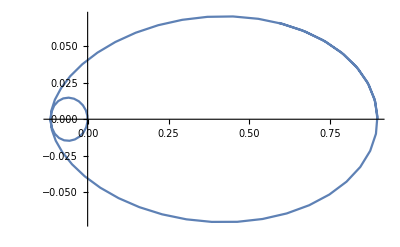

```mathematica
pBoltz[num_]:=Table[1/num,num]
pPref[ppref_,num_]:=Prepend[Table[(1-ppref)/(num-1),num-1],ppref]
n=4;
r=0.9; ρeff=(IdentityMatrix[2]+r*({x,y,z}=Normalize[{1,0,0.1}]).Rest[NQubitBasis[1]])/2;
Hp=Sum[IdentityMatrix[2^(k-1)]⊗PauliMatrix[3]⊗PauliMatrix[3]⊗IdentityMatrix[2^(n-k-1)],{k,1,n-1}];
pvec=pBoltz[n];ρmax=MaxEntN[ρeff,pvec];
sol=NDSolveValue[{I*rho'[t]==Hp.rho[t]-rho[t].Hp,rho[0]==ρmax},rho,{t,0,end=10}];
points=Table[densityMatrixToPoint[{CGNto1[sol[t],pvec]},NQubitBasis[1]][[1]][[1;;2]],{t,0,3.5,0.05}];
ListLinePlot[points]
Clear[rho,n,r,x,y,z,points,sol,pvec,Hp]
```

```mathematica
(*Do code to create plots with several N's on them*)
Clear[n]
Clear[points]
points={};
r=0.9;
({x,y,z}=Normalize[{1,0,0.1}]);
ρeff=(IdentityMatrix[2]+r*({x,y,z}).Rest[NQubitBasis[1]])/2;
tini=0.;tend=10.;
nsequence=List[3,9,2];nvalues=Table[k,{k,nsequence[[1]],nsequence[[2]],nsequence[[3]]}];
```

```mathematica
Monitor[
n=0;
Do[
Hp=Sum[IdentityMatrix[2^(k-1)]⊗PauliMatrix[3]⊗PauliMatrix[3]⊗IdentityMatrix[2^(n-k-1)],{k,1,n-1}];
pvec=pBoltz[n]; ρmax=MaxEntN[ρeff,pvec];
sol=NDSolveValue[{I*rho'[t]==Hp.rho[t]-rho[t].Hp,rho[0.]==ρmax},rho,{t,tini,tend}];
pointstemp=Table[densityMatrixToPoint[{CGNto1[sol[t],pvec]},NQubitBasis[1]][[1]][[1;;2]],{t,0,3.5,0.05}];
AppendTo[points,pointstemp];
Clear[rho,sol,pvec,Hp,ρmax,rho],{n,nsequence[[1]],nsequence[[2]],nsequence[[3]]}
],
ProgressIndicator[n/(Length[nvalues]*nsequence[[3]])]]
```

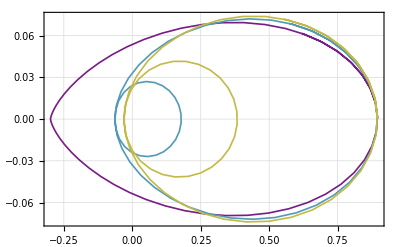

```mathematica
plot=With[{Fontsize=18},ListLinePlot[points,
PlotTheme->"FrameGrid",
FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{x}","r_{y}"},
PlotStyle->(Directive[ColorData["Rainbow"][#],Thickness[0.003]]&/@(Range[0,Length[nvalues]]/Length[nvalues])),
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize},
PlotLegends->(MaTeX[#,FontSize->Fontsize]&)/@("n="<>ToString[#]&/@nvalues),
PlotLabel->(MaTeX[#,FontSize->Fontsize]&["r="<>ToString[r]<>","<>"\\langle\\sigma_{3}\\rangle_{\\text{ef}}="<>ToString[NumberForm[z,{3,2}]]])]]
```

```mathematica
(*different p*)
label="Ising_Pref"<>"_n="<>ToString[n]<>"_p1="<>ToString[p1]<>"_z="<>ToString[NumberForm[z,{3,2}]]<>"_end="<>ToString[end];
Export[NotebookDirectory[]<>"../thesis/chapter3/figures_special/"<>label<>".png",plot]
```

```mathematica
(*equal p*)
label="Ising_Boltz"<>"_n="<>ToString[n]<>"_z="<>ToString[NumberForm[z,{3,2}]]<>"_end="<>ToString[end];
Export[NotebookDirectory[]<>"../thesis/chapter3/figures_special/"<>label<>".png",plot]
```

## Appendices

## Ap. Comparison with average assignment

### Distance Comparisons

```mathematica
distmatex="\\lVert \\mathcal{A}_{\\mathcal{C}}^{\\text{avg}}(\\rho_{\\text{ef}})-\\mathcal{A}_{\\mathcal{C}}^{\\text{max}}(\\rho_{\\text{ef}}) \\rVert_{\\text{F}}";
avgdistmatex="\\lVert \\mathcal{A}_{\\mathcal{C}}^{\\text{avg}}(\\rho_{\\text{ef}})-\\mathbb{I} \\rVert_{\\text{F}}";
maxdistmatex="\\lVert \\mathcal{A}_{\\mathcal{C}}^{\\text{max}}(\\rho_{\\text{ef}})-\\mathbb{I} \\rVert_{\\text{F}}";
```

```mathematica
points3=Table[{zef,Norm[ρaverageTwoQubitsbasiscomp[p,zef]-IdentityMatrix[4]/4,"Frobenius"]},{p,0.0,0.5,0.1},{zef,0.0,1.,0.005}]//Quiet;
dAvgOrigin=ListLinePlot[points3,
PlotTheme->"Frame",
FrameStyle->Black,
FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{\\text{ef}}",avgdistmatex},
PlotStyle->(Directive[ColorData["Rainbow"][#],Thickness[0.003]]&/@(Range[0,(points3//Dimensions)[[1]]]/(points3//Dimensions)[[1]])),
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
(*PlotLabel->(MaTeX[#,FontSize->Fontsize]&)@("\\text{Vertical lines at } p_{1}=(1-z_{\\text{ef}})/2"),*)
PlotLegends->(MaTeX[#,FontSize->Fontsize]&)/@Table["p_{1}="<>ToString[p],{p,0.0,0.5,0.1}],
GridLines->{Table[1-2*p,{p,0.0,0.5,0.1}],{}}];
Export[NotebookDirectory[]<>"../thesis/appendices/figures/"<>"dist_avg_or_vs_p"<>".png",dAvgOrigin]
```

```mathematica
points4=Table[{zef,Norm[MaxEntN[ (IdentityMatrix[2]+zef*PauliMatrix[3])/2,{p,1-p}]-IdentityMatrix[4]/4,"Frobenius"]},{p,0.0,0.5,0.1},{zef,0.0,1.,0.005}]//Quiet;
dMaxEntOrigin=ListLinePlot[points4,
PlotTheme->"Frame",
FrameStyle->Black,
FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{\\text{ef}}",maxdistmatex},
PlotStyle->(Directive[ColorData["Rainbow"][#],Thickness[0.003]]&/@(Range[0,(points4//Dimensions)[[1]]]/(points4//Dimensions)[[1]])),
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
(*PlotLabel->(MaTeX[#,FontSize->Fontsize]&)@("\\text{Vertical lines at } p_{1}=(1-z_{\\text{ef}})/2"),*)
PlotLegends->(MaTeX[#,FontSize->Fontsize]&)/@Table["p_{1}="<>ToString[p],{p,0.0,0.5,0.1}],
GridLines->{Table[1-2*p,{p,0.0,0.5,0.1}],{}}]
Export[NotebookDirectory[]<>"../thesis/appendices/figures/"<>"dist_maxent_or_vs_p"<>".png",dMaxEntOrigin]
```

```mathematica
Fontsize=18;
points2=Table[{zef,Norm[ρaverageTwoQubitsbasiscomp[p,zef]-MaxEntN[ (IdentityMatrix[2]+zef*PauliMatrix[3])/2,{p,1-p}],"Frobenius"]},{p,0.0,0.5,0.1},{zef,0.0,1.,0.005}]//Quiet;
dMaxEntAvgZ=ListLinePlot[points2,
PlotTheme->"Frame",
FrameStyle->Black,
FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{\\text{ef}}",""},
PlotStyle->(Directive[ColorData["Rainbow"][#],Thickness[0.003]]&/@(Range[0,(points2//Dimensions)[[1]]]/(points2//Dimensions)[[1]])),
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
(*PlotLabel->(MaTeX[#,FontSize->Fontsize]&)@("\\text{Vertical lines at } z_{\\text{ef}}=1-2p_{1}"),*)
PlotLegends->(MaTeX[#,FontSize->Fontsize]&)/@Table["p_{1}="<>ToString[p],{p,0.0,0.5,0.1}],
GridLines->{Table[1-2*p,{p,0.0,0.5,0.1}],{}}]
Export[NotebookDirectory[]<>"../thesis/appendices/figures/"<>"dist_maxent_avg_vs_z"<>".png",dMaxEntAvgZ]
```

```mathematica
Fontsize=18;
points1=Table[{p,Norm[ρaverageTwoQubitsbasiscomp[p,zef]-MaxEntN[ (IdentityMatrix[2]+zef*PauliMatrix[3])/2,{p,1-p}],"Frobenius"]},{zef,0.,1.,0.2},{p,0,0.5,0.001}]//Quiet;
dMaxEntAvgP=ListLinePlot[points1,
PlotTheme->"Frame",
FrameStyle->Black,
FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"p_{1}",distmatex},
PlotStyle->(Directive[ColorData["Rainbow"][#],Thickness[0.003]]&/@(Range[0,(points1//Dimensions)[[1]]]/(points1//Dimensions)[[1]])),
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize-5},
(*PlotLabel->(MaTeX[#,FontSize->Fontsize]&)@("\\text{Vertical lines at } p_{1}=(1-z_{\\text{ef}})/2"),*)
PlotLegends->(MaTeX[#,FontSize->Fontsize]&)/@Table["r_{\\text{ef}}="<>ToString[zef],{zef,0.,1.,0.2}],
GridLines->{Table[(1-zef)/2,{zef,0.,1.,0.2}],{}}]
Export[NotebookDirectory[]<>"../thesis/appendices/figures/"<>"dist_maxent_avg_vs_p"<>".png",dMaxEntAvgP]
```

```mathematica
p=0.0;
zef=1.;
rhoav=ρaverageTwoQubitsbasiscomp[p,zef]
CGNto1[rhoav,{p,1-p}]
MaxEntN[ (IdentityMatrix[2]+zef*PauliMatrix[3])/2,{p,1-p}]
Norm[ρaverageTwoQubitsbasiscomp[p,zef]-MaxEntN[ (IdentityMatrix[2]+zef*PauliMatrix[3])/2,{p,1-p}],"Frobenius"]
Clear[p,zef]
```

### Dynamics Comparisons

#### Local Evolutions

```mathematica
ω={Pi,3*Pi};
Ham1=KroneckerProduct[PauliMatrix[3],IdentityMatrix[2]];
Ham2=KroneckerProduct[IdentityMatrix[2],PauliMatrix[3]];
H=ω.{Ham1,Ham2};
U[t_]:=MatrixExp[-I*t*H];
```

```mathematica
p=0.1;
ρef = Chop[(IdentityMatrix[2] + (rp=0.9)* ({x,y,z}=Normalize[{1., 0., 0.1}]).Rest[NQubitBasis[1]])/2];
ref = densityMatrixToPoint[{ρef}, NQubitBasis[1]];
Urot=UnitaryToRotateFineStates[ρef];
ρavg=Chop[Urot.ρaverageTwoQubitsbasiscomp[p,rp].Dagger[Urot]];
ρmax=MaxEntN[ρef,{p,1-p}];
CGNto1[ρavg,{p,1-p}]==ρef
```

```mathematica
evρavg[t_]:=CGNto1[U[t].ρavg.Dagger[U[t]],{p,1-p}]
evρmax[t_]:=CGNto1[U[t].ρmax.Dagger[U[t]],{p,1-p}]
```

```mathematica
avgvsmax=ParametricPlot[{densityMatrixToPoint[{evρavg[t]},NQubitBasis[1]][[1]][[1;;2]],densityMatrixToPoint[{evρmax[t]},NQubitBasis[1]][[1]][[1;;2]]},{t,0,1.},
PlotRange->All,
PlotTheme->"FrameGrid",
FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{x}","r_{y}"},
PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Black}},
FrameStyle->Black,
PlotRange->All,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize},
PlotLegends->Placed[(MaTeX[#,FontSize->Fontsize]&)/@{"\\vec{r}_{\\text{ef}}^{\\,\\text{ avg}}(t)","\\vec{r}_{\\text{ef}}^{\\,\\text{ max}}(t)"},{0.7,0.6}],
Epilog->{Darker[Green],PointSize[0.02],Point[densityMatrixToPoint[{evρavg[0]},NQubitBasis[1]][[1]][[1;;2]]]}];
```

```mathematica
Export["../thesis/appendices/figures/local_AvgVSMax_p2="<>ToString[p]<>"_r="<>ToString[rp]<>"_w1="<>ToString[ω[[1]]/Pi]<>"_w2="<>ToString[ω[[2]]/Pi]<>".png",avgvsmax]
```

#### SWAP Gate

```mathematica
p=0.1;
ρef = Chop[(IdentityMatrix[2] + (rp=0.9)* ({x,y,z}=Normalize[{1., 0., 0.1}]).Rest[NQubitBasis[1]])/2];
ρef2 = Chop[(IdentityMatrix[2] + (rp=0.9)* ({x,y,z}=Normalize[{0., 1., 0.1}]).Rest[NQubitBasis[1]])/2];
ref = densityMatrixToPoint[{ρef}, NQubitBasis[1]];
Urot=UnitaryToRotateFineStates[ρef];
ρavg=Chop[Urot.ρaverageTwoQubitsbasiscomp[p,rp].Dagger[Urot]];
ρmax=MaxEntN[ρef2 ,{p,1-p}];
CGNto1[ρavg,{p,1-p}]==ρef
```

```mathematica
evρavg[t_]:=CGNto1[SWAP[t].ρavg.Dagger[SWAP[t]],{p,1-p}]
evρmax[t_]:=CGNto1[SWAP[t].ρmax.Dagger[SWAP[t]],{p,1-p}]
```

```mathematica
avgvsmax=ParametricPlot[{densityMatrixToPoint[{evρavg[t]},NQubitBasis[1]][[1]][[1;;2]],densityMatrixToPoint[{evρmax[t]},NQubitBasis[1]][[1]][[1;;2]]},{t,0,2.},
PlotRange->All,
PlotTheme->"FrameGrid",
FrameLabel->(MaTeX[#,FontSize->Fontsize]&)/@{"r_{x}","r_{y}"},
PlotStyle->{{Thickness[0.003],Red},{Thickness[0.003],Black}},
FrameStyle->Black,
PlotRange->All,
LabelStyle->{FontFamily->"Latin Modern Roman",Black,FontSize->Fontsize},
PlotLegends->Placed[(MaTeX[#,FontSize->Fontsize]&)/@{"\\vec{r}_{\\text{ef}}^{\\,\\text{ avg}}(t)","\\vec{r}_{\\text{ef}}^{\\,\\text{ max}}(t)"},{0.7,0.6}],
Epilog->{Darker[Red],PointSize[0.02],Point[densityMatrixToPoint[{evρavg[0]},NQubitBasis[1]][[1]][[1;;2]]],Black,PointSize[0.02],Point[densityMatrixToPoint[{evρmax[0]},NQubitBasis[1]][[1]][[1;;2]]]}]
```

## Ap. My first differential equation

### Some preliminaries, a simple example

```mathematica
Mt[t_]:=(IdentityMatrix[3]+{{Cos[2*t],-Sin[2*t],0},{Sin[2*t],Cos[2*t],0},{0,0,1}})/2; (*La evolucion no diferencial*)
incon=RandomReal[]*Normalize[Table[RandomReal[],3]]; (*Condicion incial aleatoria*)
s=NDSolve[{{x1'[t],x2'[t],x3'[t]}==H3[t].{x1[t],x2[t],x3[t]},x1[0]==incon[[1]],x2[0]==incon[[2]],x3[0]==incon[[3]]},{x1[t],x2[t],x3[t]},{t,0,π/2}]; (*evolucion diferencial*)
Plot[Norm[Mt[t].incon-{x1[t],x2[t],x3[t]}/.s],{t,0,Pi/2},PlotRange->All]
Plot[{M[t].incon,{x1[t],x2[t],x3[t]}/.s},{t,0,Pi/2},PlotRange->All,PlotLegends->Placed[{"M","Dif"},{0.8,0.7}]]
```

```mathematica
Inverse[{{1,0,0},{0,(1+Exp[-I*t])/2,0},{0,0,1}}]
```

```mathematica
(*Vectorizing and devectorizing functions*)
VectorizeDO[do_]:=Flatten[do];
Devectorized[do_,shape_]:=ArrayReshape[do,shape];
shape1={2,2};
shape2={4,4};

(*Unitary, hamiltonian, rho(t), and superoperator*)
Ut=KroneckerProduct[IdentityMatrix[2],MatrixExp[-I*PauliMatrix[3]]];
Ham=KroneckerProduct[IdentityMatrix[2],PauliMatrix[3]];
rhot={{r00,r01},{r10,r11}};
Gt={{1,0,0,0},
{0,(1+Exp[-I*t])/2,0,0},
{0,0,(1+Exp[I*t])/2,0},
{0,0,0,1}};
Gtinv=Inverse[Gt]//FullSimplify;

(*Assignement map*)
Assign[do_]:=KroneckerProduct[do,do];

(*First, apply inverse dynamics to vectorized density operator, then get assmap*)
asst=Assign[Devectorized[Gtinv.VectorizeDO[rhot],shape1]]//FullSimplify;
(*Evolve the result using the unitary dynamics*)
evass=Ut.asst.Dagger[Ut]//FullSimplify;
(*Calculate the commutator with the hamiltonian*)
conm=Commutator[Ham,evass]//FullSimplify;
(*Take the CG*)
dev=(CGKraus[conm,1/2]//FullSimplify)/.(r00+r11->1);
VectorizeDO[dev]//MatrixForm
```

```mathematica
TM={{1,0,0,1},{0,1,-I,0},{0,1,I,0},{1,0,0,-1}}/2;
MT=Inverse[TM];
rhop={1,x,y,z}
Devectorized[TM.rhop,shape1]//MatrixForm;
HP={{0,0,0,0},{0,-Tan[t],-1,0},{0,1,-Tan[t],0},{0,0,0,0}};
TM.HP.MT//FullSimplify
```

### Another example, an equation for the microscopic SWAP

```mathematica
H=I*MatrixLog[SWAP[1]]
```

```mathematica
(*Vectorizing and devectorizing functions*)
VectorizeDO[do_]:=Flatten[do];
Devectorized[do_,shape_]:=ArrayReshape[do,shape];
shape1={2,2};
shape2={4,4};

(*Unitary, hamiltonian, rho(t), and superoperator*)
Ut=SWAP[t];
Ham=H;
rhot={{r00,r01},{r10,r11}};
Gt={{1,0,0,0},
{0,(1+Exp[-I*t])/2,0,0},
{0,0,(1+Exp[I*t])/2,0},
{0,0,0,1}};
Gtinv=Inverse[Gt]//FullSimplify;

(*Assignement map*)
Assign[do_]:=KroneckerProduct[do,do];

(*First, apply inverse dynamics to vectorized density operator, then get assmap*)
asst=Assign[Devectorized[Gtinv.VectorizeDO[rhot],shape1]]//FullSimplify;
(*Evolve the result using the unitary dynamics*)
evass=Ut.asst.Dagger[Ut]//FullSimplify;
(*Calculate the commutator with the hamiltonian*)
conm=Commutator[Ham,evass]//FullSimplify;
(*Take the CG*)
dev=(CGKraus[conm,1/2]//FullSimplify)/.(r00+r11->1);
VectorizeDO[dev]//MatrixForm
```

```mathematica
BoltzmannClone[rho_]:=KroneckerProduct[rho,rho];
rho={{r00,r01},{r10,r11}};
ev=Refine[SWAP[t].BoltzmannClone[rho].Dagger[SWAP[t]],{Element[t,Reals]}]//FullSimplify;
ev==BoltzmannClone[rhot]
```

```mathematica
SWAP[t]//MatrixForm
```

```mathematica
Refine[SWAP[t].BoltzmannClone[rhot].Dagger[SWAP[t]],{Element[t,Reals]}]
```

```mathematica
Depolarizing[rho_,lam_]:=(1-lam)*IdentityMatrix[2]/2+lam*rho;
rho={{r00,r01},{r10,r11}};
Depolarizing[Depolarizing[rho,1/λ],λ]//FullSimplify
```

```mathematica
I*MatrixExp[-I*PauliMatrix[3]*Pi/2]
```

```mathematica
MaxEnt[rhovec_,p_]:=With[{vecA=MapAt[#*p*Tanh[p*λ]/r&,rhovec,{{2},{3},{4}}],vecB=MapAt[#*(1-p)*Tanh[(1-p)*λ]/r&,rhovec,{{2},{3},{4}}]},Flatten[KroneckerProduct[vecA,vecB]]];
vec={1,x,y,z};
inv[vec_,κ_]:=MapAt[#/κ&,vec,{{2},{3},{4}}]

inv[vec,κ]
psi0vec=MaxEnt[inv[vec,κ],p];
psi0=psi0vec.gellMannBasis[2]/2//FullSimplify;
```

```mathematica
psit=Refine[SWAP[t].psi0.Dagger[SWAP[t]],{Element[t,Reals],Element[p,Reals]}]//FullSimplify;
```

```mathematica
conm=Commutator[I*MatrixLog[SWAP[1]],psit];
dev=CGKraus[conm,p]//FullSimplify;
```

```mathematica
change=Refine[densityMatrixToPoint[{dev},gellMannBasis[1]],{Element[t,Reals],Element[p,Reals]}][[1]]//FullSimplify;
```

```mathematica
Refine[change,{0<p<1}]//FullSimplify//MatrixForm
```

```mathematica
densityMatrixToPoint[{SWAP[1]},gellMannBasis[2]][[1]]
```

```mathematica
Sum[LeviCivitaTensor[3][[i,j,3]],{i,3},{j,3}]
```

```mathematica
sumsigma=Sum[KroneckerProduct[PauliMatrix[i],PauliMatrix[i]],{i,3}]/2
```

```mathematica
rep[mat_]:=densityMatrixToPoint[{mat},gellMannBasis[2]][[1]]/(2*Sqrt[2.])
dotpower[mat_,n_]:=Nest[#.mat&,mat,n]
```

```mathematica
dotpower[sumsigma,1]
```

```mathematica
rep[sumsigma.sumsigma.sumsigma.sumsigma]
```

```mathematica
2*Sqrt[2.]
```

```mathematica
SWAP[t]//MatrixForm
```

```mathematica
densityMatrixToPoint[{SWAP[t]},gellMannBasis[2]][[1]]//MatrixForm
```

```mathematica
I*densityMatrixToPoint[{MatrixLog[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}]},gellMannBasis[2]]
```

```mathematica
H={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}};
U[t_]:=MatrixExp[-I*t*H];
rho={{r00,r01},{r10,r11}};;
psi=KroneckerProduct[rho,rho];
psit=Refine[U[t].psi.Dagger[U[t]],{Element[t,Reals]}];
rhot=CGKraus[psit,1/2]//FullSimplify//MatrixForm
```

```mathematica
densityMatrixToPoint[{rhot},gellMannBasis[1]][[1]]//FullSimplify//MatrixForm
```

```mathematica
OBTAIN IMAGE OF THE EVOLUTION
```

```mathematica
Inverse[(IdentityMatrix[3]*(1+z)+-(z-1)*{{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}})/2]//FullSimplify//MatrixForm
```

```mathematica
Plot[{Sin[2x],Cos[x]^2-Sin[x]^2},{x,0,10}]
```